```mathematica
Integrate[1/(z - r1) + 1/(z-r2)+1/(z- ⅈ r3)+1/(z+ ⅈ r3),z]
```

Log[-r1+z]+Log[-r2+z]+Log[-ⅈ r3+z]+Log[ⅈ r3+z]

```mathematica
Integrate[1/(z - r1) * 1/(z-r2)*1/(z- ⅈ r3)*1/(z+ ⅈ r3),z]
```

(-2 (r1^2 r2+r2 r3^2-r1 (r2^2+r3^2)) ArcTan[r3/z]+r3 (2 (r2^2+r3^2) Log[-r1+z]-2 (r1^2+r3^2) Log[-r2+z]+(r1^2-r2^2) Log[r3^2+z^2]))/(2 (r1-r2) (r1-ⅈ r3) (r2-ⅈ r3) (r1+ⅈ r3) (r2+ⅈ r3) r3)

```mathematica
FindRoot[z^4+0.01/(4/300)*z - (.01*0.4+(4/300))/(4/300),{z,0.8}]
```

{z→0.89142}

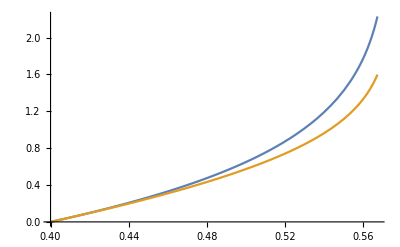

```mathematica
Plot[{NIntegrate[-1/(z^4+0.01/(4/300)*z - (.01*0.4+(4/300)*0.7^4)/(4/300)),{z,0.4,t}],(-(a (-T0+Teq)^(1/4))/(cv T0+a T0^4-U)*(t-T0))/((0.57716788-t)^(1/4))/.{U-> a Tr0^4+ Cv T0}/.{a-> 0.0137202,c-> 30.,Cv->0.01,cv-> 0.01,σ-> 100,Tr0-> 0.7,T0-> 0.4,Teq-> 0.57716788}},{t,0.4,0.57716788-0.01},PlotRange->All]
```

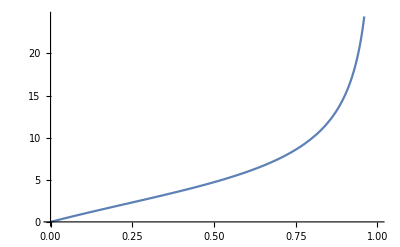

```mathematica
Plot[10 x/(1+x)/Sqrt[(0.8914196575145653-x)],{x,0,1}]
```

```mathematica
4*100/0.01
```

40000.

```mathematica
tsol=NDSolve[{T'[t] == -c σ/Cv(-U/a+Cv/a T[t] + T[t]^4),T[0]== T0}/.{U-> a Tr0^4+ Cv T0}/.{a-> 0.0137202,c-> 30.,Cv-> 0.01,σ-> 10,Tr0-> 1.0,T0-> 0.4},T[t],{t,0,1},MaxStepSize->1/40000]
```

{{T[t]→InterpolatingFunction[{{0., 1.}}, <>][t]}}

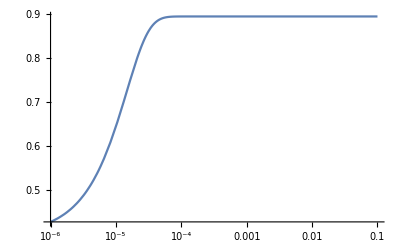

```mathematica
LogLinearPlot[Evaluate[T[t]/.tsol],{t,10^-6,0.1},PlotRange->All]
```

```mathematica
N[3^4*(4/300)]
```

1.08

```mathematica
nn=Normal[Series[1/(z^4 + cv/a z - U/a),{z,T0,0}]]
```

1/((cv T0)/a+T0^4-U/a)

```mathematica
Series[1/(z^4 + cv/a z - U/a),{z,T0,1}]
```

1/((cv T0)/a+T0^4-U/a)-(a (cv+4 a T0^3) (z-T0))/((cv T0+a T0^4-U)^2)+O[z-T0]^2

```mathematica
FullSimplify[Integrate[nn,{z,T0,t}]]/.T0-> Subscript[T, 0]
```

(a (t-T_0))/(-U+cv T_0+a T_0^4)

```mathematica
TeXForm[%]
```

\frac{a \left(t-T_0\right)}{a T_0^4+\text{cv} T_0-U}

```mathematica
Series[1/(6 (cv T0+a T0^4-U)^3)a (t-T0) (cv^2 (2 t^2-7 t T0+11 T0^2)+2 a^2 T0^6 (10 t^2-26 t T0+19 T0^2)+a cv T0^3 (4 t^2-23 t T0+31 T0^2)+3 cv (t-5 T0) U-12 a T0^2 (-t^2+t T0+T0^2) U+6 U^2),{t,T0,2}]
```

(a (t-T0))/(cv T0+a T0^4-U)-((a (cv+4 a T0^3)) (t-T0)^2)/(2 (cv T0+a T0^4-U)^2)+O[t-T0]^3

```mathematica
Series[(A*0+B( t-T0))/((Teq-t)^(1/4)),{t,T0,2}]
```

(B (t-T0))/(-T0+Teq)^(1/4)+(B (t-T0)^2)/(4 (-T0+Teq)^(5/4))+O[t-T0]^3

```mathematica
Series[(t-T)^(1/4),{t,0,1}]
```

(-T)^(1/4)-((-T)^(1/4) t)/(4 T)+O[t]^2

```mathematica
D[(t-T)^(1/4),t]
```

1/(4 (t-T)^(3/4))

```mathematica
Solve[(t-T0)/((cv T0)/a+T0^4-U/a)== (B (t-T0))/(-T0+Teq)^(1/4),B]
```

{{B→(a (-T0+Teq)^(1/4))/(cv T0+a T0^4-U)}}

```mathematica
TeXForm[(a (-T0+Teq)^(1/4))/(cv T0+a T0^4-U)/.{Teq-> Subscript[T, eq],T0-> Subscript[T, 0]}]
```

\frac{a \sqrt[4]{T_{\text{eq}}-T_0}}{a T_0^4+\text{cv} T_0-U}

```mathematica
D[x HeavisideTheta[x]*-1 + 2 x*HeavisideTheta[-x],x]
```

-3 x DiracDelta[x]+2 HeavisideTheta[-x]-HeavisideTheta[x]

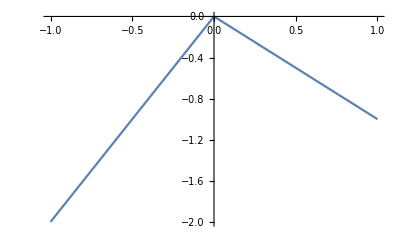

```mathematica
Plot[x HeavisideTheta[x]*-1 + 2 x*HeavisideTheta[-x],{x,-1,1}]
```

```mathematica
Assuming[t<r,Integrate[-1/((T-1)T^3),{T,1/10,t}]]
```

ConditionalExpression[60-(1+2 t)/(2 t^2)+Log[-(9 t)/(-1+t)], 0<t<1]

```mathematica
D[Log[-(9 t)/(-1+t)],t]
```

-((-1+t) (-9/(-1+t)+(9 t)/(-1+t)^2))/(9 t)

```mathematica
Integrate[Series[1/((T-r)*T^3),{T,r,2}],T]
```

Log[-r+T]/r^3-(3 (T-r))/r^4+(3 (T-r)^2)/r^5-(10 (T-r)^3)/(3 r^6)+O[T-r]^4

```mathematica
Solve[(Teq-t)/(t-T0)==c^4,t]
```

{{t→(c^4 T0+Teq)/(1+c^4)}}

```mathematica
Integrate[1/(z-r)^4,z]
```

1/(3 (r-z)^3)

```mathematica
Series[1/(3 (r-z)^3),{z,r,2}]
```

-1/(3 (z-r)^3)+O[z-r]^3

```mathematica
Plot[{NIntegrate[-1/(z^4+0.01/(4/300)*z - (.01*0.4+(4/300))/(4/300)),{z,0.4,t}],(-(a (-T0+Teq)^(1/4))/(cv T0+a T0^4-U)*(t-T0))/((0.8914196575145653-t)^(1/4))/.{U-> a Tr0^4+ Cv T0}/.{a-> 0.0137202,c-> 30.,Cv->0.01,cv-> 0.01,σ-> 10,Tr0-> 1.0,T0-> 0.4,Teq-> 0.8914196575145653}},{t,0.4,0.8914196575145653-0.001},PlotRange->All]
```